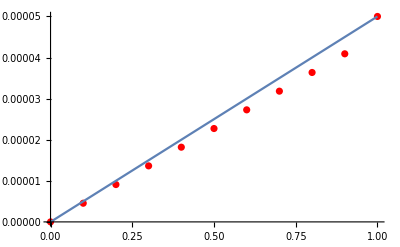

```mathematica
k=ReadList["C:\\Users\\vbole\\Desktop\\Study\\Kurs6\\out.txt", {Number, Number}];
boardCond = 0.00005;
exactSol[t_]:= boardCond  * t; 
plot = ListPlot[k, PlotStyle->Red];
plot1 =Plot[exactSol[x],{x, 0,1}];
Show[plot, plot1]
```